## Normal distribution

## Implementation of an automated process for generating normal distributions, and exporting them as graphical representations.

```mathematica
ClearAll["Global*`"]
```

### Generate the normal distribution

```mathematica
fNormal[x_,xargs_]:=1/xargs[[1]]*1/(√(2π))Exp[-1/2*((x-xargs[[2]])/xargs[[1]])^2];
normalData[xargs_,xmin_,xmax_]:=Table[{x,fNormal[x,xargs]},{x,xmin,xmax,(xmax-xmin)/100}];
```

### Helper functions for exporting graphics

```mathematica
pdfimage[name_,idx_]:=StringTemplate["``_``.pdf"][name,idx];
export[path_,object_]:=Export[StringTemplate["````"][NotebookDirectory[],path],object];
batchExport[objectname_,objectList_]:=Do[export[pdfimage[objectname,i],objectList[[i]]],{i,1,Length[objectList],1}];
```

## Extract data from a list of tuples

```mathematica
extract[data_,idx_]:=data[[;;,idx]];
```

### Create tester for exporting g_fx objects

```mathematica
rCircle[]:=Graphics[{Thickness[0.01],RandomColor[],Circle[]}];
batchExport["circleGfx",Table[rCircle[],{i,3}]]
```

## Calculation for the Area Under Curve

```mathematica
auc[xargs_,left_,right_]:=Integrate[fNormal[x,xargs],{x,left,right}];
aucN[xargs_,left_,right_]:=NIntegrate[fNormal[x,xargs],{x,left,right}];
```

## Implementation of the plotting function

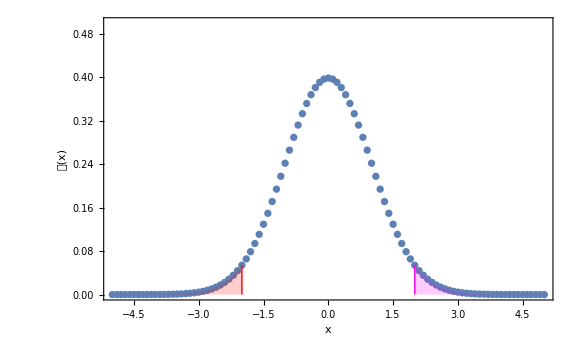

```mathematica
lines[xargs_,left_,right_]:=Graphics[{{Thick,Red,Line[{{left,0},{left,fNormal[left,xargs]}}]},{Thick,Magenta,Line[{{right,0},{right,fNormal[right,xargs]}}]}}];
leftTail[xargs_,xleft_,left_]:=Plot[fNormal[x,xargs],{x,xleft,left},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Red],PlotRange->Full];
rightTail[xargs_,xright_,right_]:=Plot[fNormal[x,xargs],{x,right,xright},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Magenta],PlotRange->Full];
plotter[data_,xargs_,left_,right_]:=ListPlot[data,ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"x","𝒫(x)"},PlotRange->{0,0.5}];
Show[plotter[normalData[{1,0},-5,5],{1,0},-2,2],lines[{1,0},-2,2],leftTail[{1,0},-5,-2],rightTail[{1,0},2,5]]
```

```mathematica
extract[normalData[{1,0},-5,5],2]
```

{1/(ⅇ^(25/2) √(2 π)),1/(ⅇ^(2401/200) √(2 π)),1/(ⅇ^(288/25) √(2 π)),1/(ⅇ^(2209/200) √(2 π)),1/(ⅇ^(529/50) √(2 π)),1/(ⅇ^(81/8) √(2 π)),1/(ⅇ^(242/25) √(2 π)),1/(ⅇ^(1849/200) √(2 π)),1/(ⅇ^(441/50) √(2 π)),1/(ⅇ^(1681/200) √(2 π)),1/(ⅇ^8 √(2 π)),1/(ⅇ^(1521/200) √(2 π)),1/(ⅇ^(361/50) √(2 π)),1/(ⅇ^(1369/200) √(2 π)),1/(ⅇ^(162/25) √(2 π)),1/(ⅇ^(49/8) √(2 π)),1/(ⅇ^(289/50) √(2 π)),1/(ⅇ^(1089/200) √(2 π)),1/(ⅇ^(128/25) √(2 π)),1/(ⅇ^(961/200) √(2 π)),1/(ⅇ^(9/2) √(2 π)),1/(ⅇ^(841/200) √(2 π)),1/(ⅇ^(98/25) √(2 π)),1/(ⅇ^(729/200) √(2 π)),1/(ⅇ^(169/50) √(2 π)),1/(ⅇ^(25/8) √(2 π)),1/(ⅇ^(72/25) √(2 π)),1/(ⅇ^(529/200) √(2 π)),1/(ⅇ^(121/50) √(2 π)),1/(ⅇ^(441/200) √(2 π)),1/(ⅇ^2 √(2 π)),1/(ⅇ^(361/200) √(2 π)),1/(ⅇ^(81/50) √(2 π)),1/(ⅇ^(289/200) √(2 π)),1/(ⅇ^(32/25) √(2 π)),1/(ⅇ^(9/8) √(2 π)),1/(ⅇ^(49/50) √(2 π)),1/(ⅇ^(169/200) √(2 π)),1/(ⅇ^(18/25) √(2 π)),1/(ⅇ^(121/200) √(2 π)),1/(√(2 ⅇ π)),1/(ⅇ^(81/200) √(2 π)),1/(ⅇ^(8/25) √(2 π)),1/(ⅇ^(49/200) √(2 π)),1/(ⅇ^(9/50) √(2 π)),1/(ⅇ^(1/8) √(2 π)),1/(ⅇ^(2/25) √(2 π)),1/(ⅇ^(9/200) √(2 π)),1/(ⅇ^(1/50) √(2 π)),1/(ⅇ^(1/200) √(2 π)),1/(√(2 π)),1/(ⅇ^(1/200) √(2 π)),1/(ⅇ^(1/50) √(2 π)),1/(ⅇ^(9/200) √(2 π)),1/(ⅇ^(2/25) √(2 π)),1/(ⅇ^(1/8) √(2 π)),1/(ⅇ^(9/50) √(2 π)),1/(ⅇ^(49/200) √(2 π)),1/(ⅇ^(8/25) √(2 π)),1/(ⅇ^(81/200) √(2 π)),1/(√(2 ⅇ π)),1/(ⅇ^(121/200) √(2 π)),1/(ⅇ^(18/25) √(2 π)),1/(ⅇ^(169/200) √(2 π)),1/(ⅇ^(49/50) √(2 π)),1/(ⅇ^(9/8) √(2 π)),1/(ⅇ^(32/25) √(2 π)),1/(ⅇ^(289/200) √(2 π)),1/(ⅇ^(81/50) √(2 π)),1/(ⅇ^(361/200) √(2 π)),1/(ⅇ^2 √(2 π)),1/(ⅇ^(441/200) √(2 π)),1/(ⅇ^(121/50) √(2 π)),1/(ⅇ^(529/200) √(2 π)),1/(ⅇ^(72/25) √(2 π)),1/(ⅇ^(25/8) √(2 π)),1/(ⅇ^(169/50) √(2 π)),1/(ⅇ^(729/200) √(2 π)),1/(ⅇ^(98/25) √(2 π)),1/(ⅇ^(841/200) √(2 π)),1/(ⅇ^(9/2) √(2 π)),1/(ⅇ^(961/200) √(2 π)),1/(ⅇ^(128/25) √(2 π)),1/(ⅇ^(1089/200) √(2 π)),1/(ⅇ^(289/50) √(2 π)),1/(ⅇ^(49/8) √(2 π)),1/(ⅇ^(162/25) √(2 π)),1/(ⅇ^(1369/200) √(2 π)),1/(ⅇ^(361/50) √(2 π)),1/(ⅇ^(1521/200) √(2 π)),1/(ⅇ^8 √(2 π)),1/(ⅇ^(1681/200) √(2 π)),1/(ⅇ^(441/50) √(2 π)),1/(ⅇ^(1849/200) √(2 π)),1/(ⅇ^(242/25) √(2 π)),1/(ⅇ^(81/8) √(2 π)),1/(ⅇ^(529/50) √(2 π)),1/(ⅇ^(2209/200) √(2 π)),1/(ⅇ^(288/25) √(2 π)),1/(ⅇ^(2401/200) √(2 π)),1/(ⅇ^(25/2) √(2 π))}